```mathematica
F2[x_,y_] := √2((1-x)*(1-y)+x*y)
F3[x_,y_,z_]:=2((1-x)*(1-y)*(1-z)+x*y*z)
F4[x_,y_,z_,w_]:=2 √2((1-x)*(1-y)*(1-z)*(1-w)+x*y*z*w)
```

```mathematica
Fn[a__]:= (Times @@ a + Times @@ (1-a))*2^((Length[a]-1)/2)
Fn[{p1,p2}]+Fn[{1-p1,p2}]+Fn[{p1,1-p2}]+Fn[{1-p1,1-p2}]
```

```mathematica
Fn[{0.3,0.3,1/2}]
```

0.58

```mathematica
Fn[{0.3,.3}]
```

```mathematica
0.8202438661763951/√2
```

0.58

```mathematica
Simplify[2 √2 (p1 (1-p2)+(1-p1) p2)+2 √2 ((1-p1) (1-p2)+p1 p2)]
```

2 √2

```mathematica
(√((1-p1)/p1)+√(p1/(1-p1)))*(√((1-p2)/p2)+√(p2/(1-p2)))
```

(√((1-p1)/p1)+√(p1/(1-p1))) (√((1-p2)/p2)+√(p2/(1-p2)))

```mathematica
Solve[F2[x,y]==F3[x,y,z],{z}]
```

{{z→(-2+√2+2 x-√2 x+2 y-√2 y-2 x y+2 √2 x y)/(2 (-1+x+y))}}

```mathematica
Show[{{Plot3D[{0},{x,0,0.4},{y,0,0.4},PlotRange->{0,0.4},Mesh->None,PlotStyle->Opacity[0],BoundaryStyle->None]},
{ParametricPlot3D[{{y,x,(-2+√2+2 x)/(2 (-1+2 x))}},{x,0,0.293},{y,(-1+√2-√2 x+2 x^2)/(√2-4 x+4 x^2),0.4},PlotRange->{0,0.4},PlotStyle->{Directive[Cyan,Specularity[White,40],Opacity[0.6]]},Mesh->None,BoundaryStyle->{Black,Thickness[0.003]}]},
{ParametricPlot3D[{{x,(-2+√2+2 x)/(2 (-1+2 x)),z}},{x,0,0.293},{z,(-1+√2-√2 x+2 x^2)/(√2-4 x+4 x^2),0.4},PlotStyle->{Directive[Cyan,Specularity[White,40],Opacity[0.6]]},Mesh->None,BoundaryStyle->{Black,Thickness[0.003]}]},
{ParametricPlot3D[{{(-2+√2+2 x)/(2 (-1+2 x)),z,x}},{x,0,0.293},{z,(-1+√2-√2 x+2 x^2)/(√2-4 x+4 x^2),0.4},PlotStyle->{Directive[Cyan,Specularity[White,40],Opacity[0.6]]},Mesh->None,BoundaryStyle->{Black,Thickness[0.003]}]},
{ParametricPlot3D[{{x,y,(-1+2 x+2 y-2 x y)/(2 (-1+x+y))}},{x,0,0.293},{y,0,0.293},PlotRange->{0,0.4},PlotStyle->{Directive[Cyan,Specularity[White,40],Opacity[0.6]]},Mesh->None,BoundaryStyle->Black,PlotPoints->50,
RegionFunction->Function[{x,y,z},F2[x,y]<=F3[x,y,z]&&F2[x,z]<=F3[x,y,z]&&F2[z,y]<=F3[x,y,z]]]},

{ParametricPlot3D[{{x,y,(-2+√2+2 x-√2 x+2 y-√2 y-2 x y+2 √2 x y)/(2 (-1+x+y))}},{x,0,0.4},{y,0,Max[0,(√2/2-(1-x))/(2*x-1)]},PlotStyle->Opacity[0.8],PlotPoints->50,Mesh->None,BoundaryStyle->{Black,Thickness[0.003]}]},
{ParametricPlot3D[{{y,(-2+√2+2 x-√2 x+2 y-√2 y-2 x y+2 √2 x y)/(2 (-1+x+y)),x}},{x,0,0.4},{y,0,Max[0,(√2/2-(1-x))/(2*x-1)]},PlotStyle->Opacity[0.8],PlotPoints->50,Mesh->None,BoundaryStyle->{Black,Thickness[0.003]}]},
{ParametricPlot3D[{{(-2+√2+2 x-√2 x+2 y-√2 y-2 x y+2 √2 x y)/(2 (-1+x+y)),x,y}},{x,0,0.4},{y,0,Max[0,(√2/2-(1-x))/(2*x-1)]},PlotStyle->Opacity[0.7],PlotPoints->50,Mesh->None,BoundaryStyle->{Black,Thickness[0.003]}]},

{ParametricPlot3D[{{x,x,x}},{x,0.,0.4},PlotStyle->{Thickness[.005],Green}]},
{ParametricPlot3D[{{x,x,0.22}},{x,0.1,0.25},PlotStyle->{Thickness[.005],Red}]},
{ParametricPlot3D[{{x,x,x+0.15}},{x,0.1,0.2},PlotStyle->{Thickness[.005],Red}]},
{ParametricPlot3D[{{x,0.1,0.55-x}},{x,0.2,0.35},PlotStyle->{Thickness[.005],Red}]},
{ParametricPlot3D[{{.2,0.1,x}},{x,0.25,0.4},PlotStyle->{Thickness[.005],Red}]},
{Graphics3D[{PointSize[0.01],Red,Point[{0.2,0.2,0.4}]}]}},BoxRatios->{1,1,1}
]
```

-Graphics3D-

```mathematica
FindRoot[F3[x,x,x+0.15]==F2[x,x],{x,0.2}]
```

```mathematica
{x->0.13292431193238305}
```

{x→0.132924}

```mathematica
FindRoot[F3[.2,.1,x]==F2[.2,.1],{x,0.2}]
```

{x→0.281059}

```mathematica
FindRoot[F3[x,x,.22]==1,{x,0.2}]
```

{x→0.206938}

```mathematica
FindRoot[F2[x,0.1]==1,{x,0.2}]
```

{x→0.241117}

```mathematica
FindRoot[F2[0.1,0.55-x]==1,{x,0.3}]
```

{x→0.308883}

```mathematica
Show[{
RegionPlot3D[{F4[x,y,z,0]>=1&&F4[x,y,z,0]>=Max[F3[x,y,z],F3[x,y,0],F3[x,0,z],F3[0,y,z]]&&F4[x,y,z,0]>=Max[F2[x,y],F2[x,z],F2[z,y],F2[x,0],F2[0,y],F2[z,0]]},{x,0.2,0.3},{y,0.2,0.3},{z,0.2,0.3},
PlotPoints->50,
Mesh->None]}
]
```

-Graphics3D-

```mathematica
Show[{
RegionPlot3D[{F3[x,y,z]>=Max[F2[x,y],F2[x,z],F2[z,y],F2[x,1/2],F2[1/2,y],F2[z,1/2],1]},{x,0.,0.3},{y,0.,0.3},{z,0.,0.3},
PlotPoints->50,
Mesh->None]}
]
```

-Graphics3D-

```mathematica
1-{1,2,3}
```

{0,-1,-2}

```mathematica
Times @@ {4,1,2}
```

8

```mathematica
1-1/(1+Exp[-2/1.56655])
```

0.218114

```mathematica
1-1/(1+Exp[-2/1.65858])
```

0.230436

```mathematica
FindRoot[Fn[{x,x,x,x}]==1,{x,0.2}]
```

{x→0.230437}

```mathematica
y1 = ((1+Tanh[x])*Log2[1+Tanh[x]]+ (1-Tanh[x])*Log2[1-Tanh[x]])/2
```

1/2 ((Log[1-Tanh[x]] (1-Tanh[x]))/Log[2]+(Log[1+Tanh[x]] (1+Tanh[x]))/Log[2])

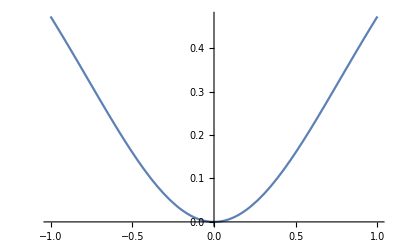

```mathematica
Plot[y,{x,-1.,1.}]
```

```mathematica
FindRoot[y1==1/2,{x,1}]
```

{x→1.04523}

```mathematica
(1+Tanh[x])/.x->1.045
```

1.77985

```mathematica
1/(1+Exp[-2*1.0490837277884566])
```

0.890725

```mathematica
NumberForm[0.8907249375573713,16]
```

0.890724937557371

```mathematica
1-0.917009
```

0.082991

```mathematica
1-0.889972
```

0.110028

```mathematica
p = (1-√(√2-1))/2
```

1/2 (1-√(-1+√2))

```mathematica
Clear[p]
```

```mathematica
K=-Log[(1-p)/p]/2
```

-1/2 Log[(1-p)/p]

```mathematica
K-0.602306378151934/.%131
```

0.000617205

```mathematica
h[p_,n_]:= ((1-p)^n+p^n)*2^((n-1)/2)
```

```mathematica
FindRoot[h[p,4]==1,{p,0.2}]
```

{p→0.230437}